# L3 Shape function and Derivates

## Isoparametric Formulation of Shape functions:

```mathematica
Quit[];
```

### L3element

Based on linear polynomial, u^e(x_) = α_0^e+α_1^e x+α_2^e x^2

```mathematica
coef = ({{Subscript[α, 0]}, {Subscript[α, 1]}, {Subscript[α, 2]}});
p[x_]:= ({{1, x, x^2}})
M= ({{1, Subscript[x, 1], Subscript[x, 1]^2}, {1, Subscript[x, 2], Subscript[x, 2]^2}, {1, Subscript[x, 3], Subscript[x, 3]^2}});
```

```mathematica
u=  p[x].coef
```

(α_2 x^2+α_1 x+α_0)

```mathematica
Ne[x_]:= p[x].Inverse[M]
```

```mathematica
Ne[x] //Simplify
```

(((x-x_2) (x-x_3))/((x_1-x_2) (x_1-x_3)) | -((x-x_1) (x-x_3))/((x_1-x_2) (x_2-x_3)) | -((x-x_1) (x-x_2))/((x_1-x_3) (x_3-x_2)))

### Test L3 element

```mathematica
Ne[Subscript[x, 1]]//Simplify
```

(1 | 0 | 0)

```mathematica
Ne[Subscript[x, 2]]//Simplify
```

(0 | 1 | 0)

```mathematica
Ne[Subscript[x, 3]]//Simplify
```

(0 | 0 | 1)

```mathematica
n = Dimensions[Ne[x]]
```

{1,3}

```mathematica
Sum[Ne[x][[1,i]],{i,1,3}] //Simplify
```

1

### L3 Isoparametric Formulation

```mathematica
(* set Subscript[x, 3]-Subscript[x, 1] = l^e, Subscript[x, 2]-Subscript[x, 1] = l^e/2, Subscript[x, 3]-Subscript[x, 2] = l^e/2 and choose l^e= 2ξ
 such that ξ(Subscript[x, 1])= -1 , ξ(Subscript[x, 2])= 0 and ξ(Subscript[x, 3])= 1 *)
(* ξ=(Subscript[x, 3]+Subscript[x, 2])/2+(Subscript[x, 3]-Subscript[x, 2])/2 x *)
```

```mathematica
x-Subscript[x, 3]= ξ-1
x-Subscript[x, 2]= ξ+0
x-Subscript[x, 1]= ξ+1
```

```mathematica
Ne[x]  /.Subscript[x, 3]-> 1-ξ+x/.Subscript[x, 2]-> -ξ+x/.Subscript[x, 1]-> -ξ-1+x//Simplify
```

(1/2 (ξ-1) ξ | 1-ξ^2 | 1/2 ξ (ξ+1))

```mathematica
NL3[ξ_]:=  ({{1/2(ξ-1)ξ, 1-ξ^2, 1/2(ξ+1)ξ}})
```

### Test L3 Isoparametric Formulation

```mathematica
NL3[-1]
NL3[0]
NL3[1]
```

(1 | 0 | 0)

(0 | 1 | 0)

(0 | 0 | 1)

```mathematica
Sum[NL3[ξ][[1,i]],{i,1,3}] //Simplify
```

1

### Plot isoparametric shape functions

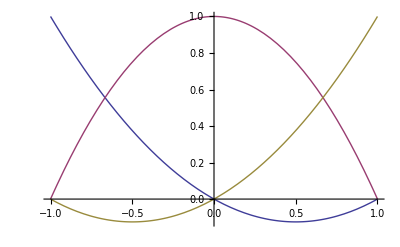

```mathematica
Plot[Tooltip[{NL3[ξ][[1,1]],NL3[ξ][[1,2]],NL3[ξ][[1,3]]}],{ξ,-1,1}]
```